# HW2 2.3 Damped Pendulum

## a)

```mathematica
A = {{0,1},{1,-s}}
Eigenvalues[A]
Eigenvectors[A]
```

{{0,1},{1,-s}}

{1/2 (-s-√(4+s^2)),1/2 (-s+√(4+s^2))}

{{1/2 (s-√(4+s^2)),1},{1/2 (s+√(4+s^2)),1}}

```mathematica
{{1,0},{-1/s,1}}
```

{{1,0},{-1/s,1}}

FP occurs when x’ and y’ = 0, this results in y = 0 and x therefore +- π/2

```mathematica
(* Determine type *)
Det[A]
Trace[A]
```

-1

{A,{{0,1},{1,-s}}}

```mathematica
{A,{{0,1},{1,-s}}}
```

{A,{{0,1},{1,-s}}}

For σ=-2 at FP(0,0) check the Eigenvectors to find out if star or degenerate node

{-1,-1}

{{-1,1},{0,0}}

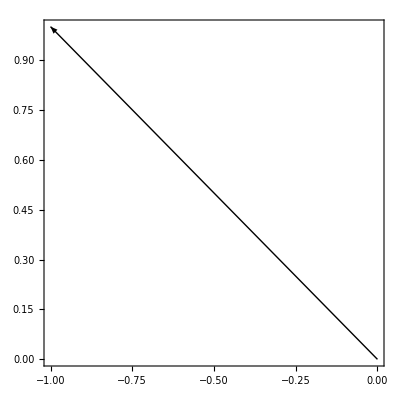

```mathematica
A = {{0,1},{-1,-2}};
eigenVL = Eigenvalues[A]
eigenvectors = Eigenvectors[A]
Graphics[{
  Arrow[{{0, 0}, #}] & /@ eigenvectors
}, Frame -> True, Axes -> True, AspectRatio -> 1, PlotRange -> All]
```

Since only one Eigenvector for this case, σ=-2 at FP(0,0) is a degenerate node, since the Eigenvalues λ = -1 it is stable

```mathematica
-Graphics-;
-Graphics-;
```

## b)

ReplaceAll::reps: {#1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

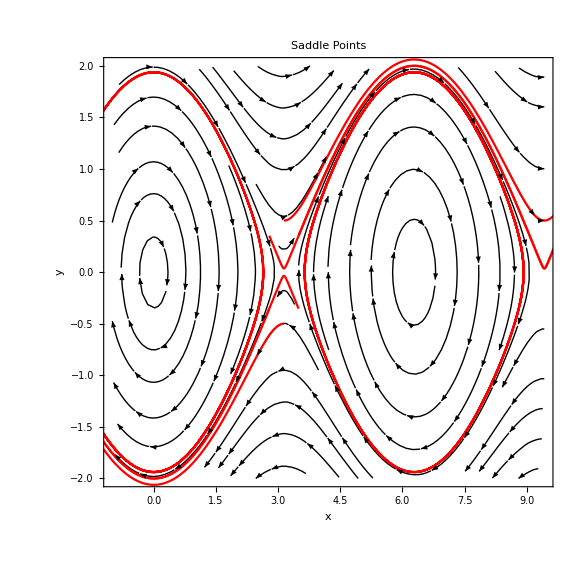

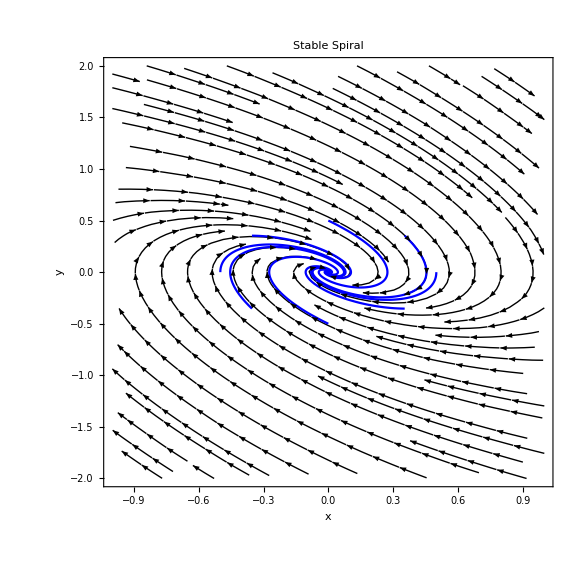

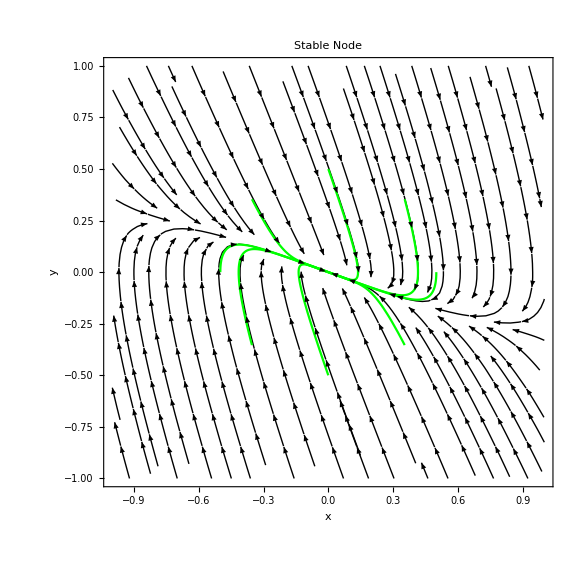

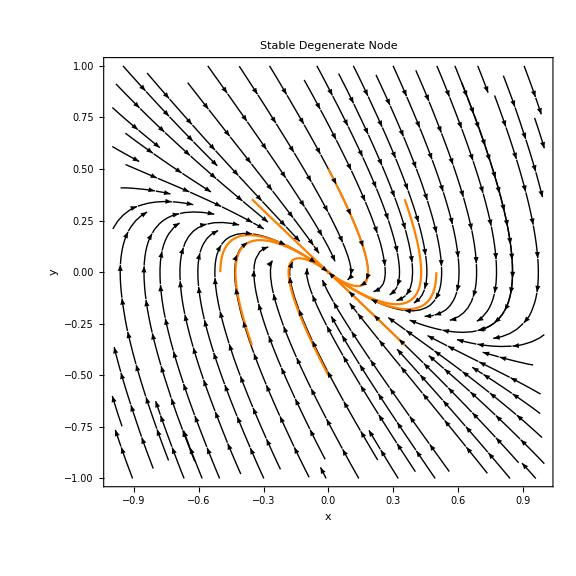

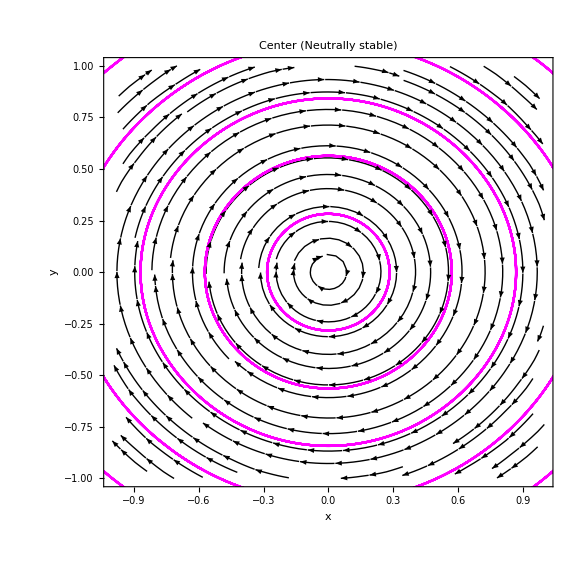

```mathematica
ClearAll["Global`*"]

(* Define the system of differential equations *)
sigma1 = 0; (* Saddle points *) 
sigma21 = 1; (* Stable Spiral *)
sigma22 = 3; (* Stable Node *) 
sigma23 = 2; (* Stable Degenerate Node *)
sigma24 = 0; (* Center *)
eq1 = x'[t] == y[t];
eq2 = y'[t] == -Sin[x[t]] - sigma1*y[t];
eq21 = y'[t] == -Sin[x[t]] - sigma21*y[t];
eq22 = y'[t] == -Sin[x[t]] - sigma22*y[t];
eq23 = y'[t] == -Sin[x[t]] - sigma23*y[t];
eq24 = y'[t] == -Sin[x[t]] - sigma24*y[t];

(* Fixed point and radius of the circular pattern *)
fixedPoint1 = {Pi, 0};
fixedPoint2 = {0, 0};
fixedPoint3 = {0, 0};

radius = 0.5;
radius3 = 0.2;

(* Define the system and the initial conditions for multiple trajectories in a circular pattern *)
system1 = {eq1, eq2};
system21 = {eq1, eq21};
system22 = {eq1, eq22};
system23 = {eq1, eq23};
system24 = {eq1, eq24};

numTrajectories = 8;

initialConditions1 = Table[{x[0] == fixedPoint1[[1]] + radius Cos[2 Pi i/numTrajectories], 
    y[0] == fixedPoint1[[2]] + radius Sin[2 Pi i/numTrajectories]}, {i, 0, numTrajectories - 1}];
initialConditions2 = Table[{x[0] == fixedPoint2[[1]] + radius Cos[2 Pi i/numTrajectories], 
    y[0] == fixedPoint2[[2]] + radius Sin[2 Pi i/numTrajectories]}, {i, 0, numTrajectories - 1}];
initialConditions3 = Table[{x[0] == fixedPoint3[[1]] + radius3 *i, 
    y[0] == fixedPoint2[[2]] + radius3 * i}, {i, 0, numTrajectories - 1}];

t0 = 0;
tMax = 40;

(* Solve the system of differential equations for multiple trajectories *)
sol1 = Table[NDSolve[{system1, initCond}, {x, y}, {t, t0, tMax}], {initCond, initialConditions1}];
sol21 = Table[NDSolve[{system21, initCond}, {x, y}, {t, t0, tMax}], {initCond, initialConditions2}];
sol22 = Table[NDSolve[{system22, initCond}, {x, y}, {t, t0, tMax}], {initCond, initialConditions2}];
sol23 = Table[NDSolve[{system23, initCond}, {x, y}, {t, t0, tMax}], {initCond, initialConditions2}];
sol24 = Table[NDSolve[{system24, initCond}, {x, y}, {t, t0, tMax}], {initCond, initialConditions3}];

(* Plot the phase portraint*) 
ps10 = StreamPlot[{y, -Sin[x] - sigma1*y}, {x, -1, 3*Pi}, {y, -2, 2}, 
   PlotRange -> All, ImageSize -> Large, ColorFunction -> (Black), 
   StreamStyle -> Directive[Black], StreamColorFunction->None];

(* Plot the phase portraint*) 
ps21 = StreamPlot[{y, -Sin[x] - sigma21*y}, {x, -1, 1}, {y, -2, 2}, 
   PlotRange -> All, ImageSize -> Large, ColorFunction -> (Black), 
   StreamStyle -> Directive[Black], StreamColorFunction->None];
ps22 = StreamPlot[{y, -Sin[x] - sigma22*y}, {x, -1, 1}, {y, -1, 1}, 
   PlotRange -> All, ImageSize -> Large, ColorFunction -> (Black), 
   StreamStyle -> Directive[Black], StreamColorFunction->None];
ps23 = StreamPlot[{y, -Sin[x] - sigma23*y}, {x, -1, 1}, {y, -1, 1}, 
   PlotRange -> All, ImageSize -> Large, ColorFunction -> (Black), 
   StreamStyle -> Directive[Black], StreamColorFunction->None];
ps24 = StreamPlot[{y, -Sin[x] - sigma24*y}, {x, -1, 1}, {y, -1, 1}, 
   PlotRange -> All, ImageSize -> Large, ColorFunction -> (Black), 
   StreamStyle -> Directive[Black], StreamColorFunction->None];
   
(* Plot trajectories for the different systems *)
p10 = ParametricPlot[Evaluate[{x[t], y[t]} /. #] & /@ sol1, {t, t0, tMax}, PlotStyle -> Red, Epilog->{Red, PointSize[0.05], Point[{Pi,0}]}];
p21 = ParametricPlot[Evaluate[{x[t], y[t]} /. #] & /@ sol21, {t, t0, tMax}, PlotStyle -> Blue, Epilog->{Red, PointSize[0.05], Point[{0,0}]}];
p22 = ParametricPlot[Evaluate[{x[t], y[t]} /. #] & /@ sol22, {t, t0, tMax}, PlotStyle -> Green, Epilog->{Red, PointSize[0.03], Point[{0,0}]}];
p23 = ParametricPlot[Evaluate[{x[t], y[t]} /. #] & /@ sol23, {t, t0, tMax}, PlotStyle -> Orange, Epilog->{Red, PointSize[0.03], Point[{0,0}]}];
p24 = ParametricPlot[Evaluate[{x[t], y[t]} /. #] & /@ sol24, {t, t0, tMax}, PlotStyle -> Magenta, Epilog->{Red, PointSize[0.03], Point[{0,0}]}];

(* Label the plot *)
Show[ps10, p10, FrameLabel -> {"x", "y"}, PlotLabel->"Saddle Points"]
Show[ps21, p21, FrameLabel -> {"x", "y"}, PlotLabel->"Stable Spiral"]
Show[ps22, p22, FrameLabel -> {"x", "y"}, PlotLabel->"Stable Node"]
Show[ps23, p23, FrameLabel -> {"x", "y"}, PlotLabel->"Stable Degenerate Node"]
Show[ps24, p24, FrameLabel -> {"x", "y"}, PlotLabel->"Center (Neutrally stable)"]
```